```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

## Examples

### Examples of creating and displaying Sessies:

Create, evolve, and display a Sessie object, saved for future reference:

```mathematica
SSSInitialState[{"ABA"->"AAB","A"->"ABA"}]
```

ABABA

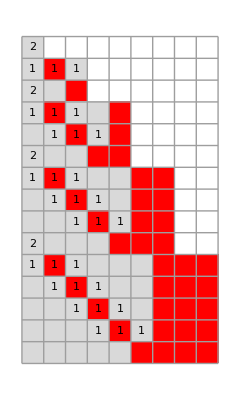


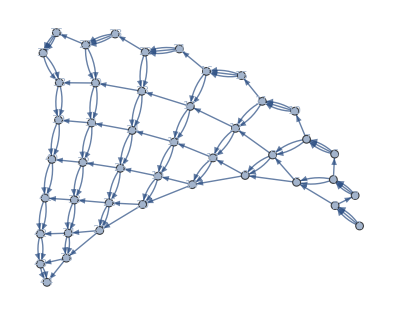
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15, NetMethod -> GraphPlot];
```

```mathematica
sss["Net"]//Sort
```

{1→2,1→2,1→2,2→3,2→5,3→4,3→4,3→4,4→5,4→5,4→6,5→8,5→9,6→7,6→7,6→7,7→8,7→8,7→10,8→9,8→9,8→12,9→13,9→14,10→11,10→11,10→11,11→12,11→12,11→15,12→13,12→13,12→17,13→14,13→14,13→18,14→19,14→20,15→16,15→16,15→16,16→17,16→17,16→21,17→18,17→18,17→23,18→19,18→19,18→24,19→20,19→20,19→25,20→26,20→27,21→22,21→22,21→22,22→23,22→23,22→28,23→24,23→24,23→30,24→25,24→25,24→31,25→26,25→26,25→32,26→27,26→27,26→33,27→34,27→35,28→29,28→29,28→29,29→30,29→30,29→36,30→31,30→31,30→38,31→32,31→32,31→39,32→33,32→33,32→40,33→34,33→34,33→41,34→35,34→35,34→42,35→43,35→44,36→37,36→37,36→37,37→38,37→38,38→39,38→39,39→40,39→40,40→41,40→41,41→42,41→42,42→43,42→43,43→44,43→44}

```mathematica
ToNetDifferenceSets[sss["Net"]]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→2,1→2,2→3,2→5,3→4,3→4,3→4,4→5,4→5,4→6,5→8,5→9,6→7,6→7,6→7,7→8,7→8,7→10,8→9,8→9,8→12,9→13,9→14,10→11,10→11,10→11,11→12,11→12,11→15,12→13,12→13,12→17,13→14,13→14,13→18,14→19,14→20,15→16,15→16,15→16,16→17,16→17,16→21,17→18,17→18,17→23,18→19,18→19,18→24,19→20,19→20,19→25,20→26,20→27,21→22,21→22,21→22,22→23,22→23,22→28,23→24,23→24,23→30,24→25,24→25,24→31,25→26,25→26,25→32,26→27,26→27,26→33,27→34,27→35,28→29,28→29,28→29,29→30,29→30,29→36,30→31,30→31,30→38,31→32,31→32,31→39,32→33,32→33,32→40,33→34,33→34,33→41,34→35,34→35,34→42,35→43,35→44,36→37,36→37,36→37,37→38,37→38,38→39,38→39,39→40,39→40,40→41,40→41,41→42,41→42,42→43,42→43,43→44,43→44}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss["Net"]]
```

Remember that each ruleset corresponds to a unique reduced enumeration index (and a unique quinary code):

```mathematica
FromReducedRankRuleSet@{"ABA"->"AAB","A"->"ABA"}
```

<|Index→253518005,QCode→343233422343,RuleSet→{ABA→AAB,A→ABA}|>

Use the enumeration index instead of the ruleset, a generic starting state string will be inserted:

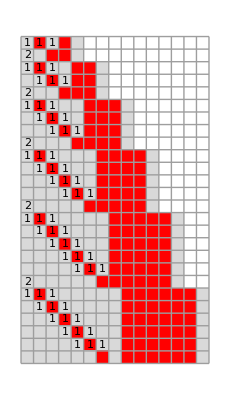
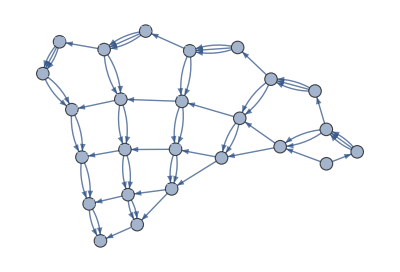
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[253518005,25,NetSize->400];
```

Look at the internal parts of the Sessie object (an Association).  Note: you will not generally want to see all this!

```mathematica
sss
```

<|Net→{1→2,1→2,1→2,2→3,3→4,3→4,3→4,4→5,4→5,2→5,4→6,6→7,6→7,6→7,7→8,7→8,5→8,8→9,8→9,5→9,7→10,10→11,10→11,10→11,11→12,11→12,8→12,12→13,12→13,9→13,13→14,13→14,9→14,11→15,15→16,15→16,15→16,16→17,16→17,12→17,17→18,17→18,13→18,18→19,18→19,14→19,19→20,19→20,14→20,16→21,21→22,21→22,21→22,22→23,22→23,17→23,23→24,23→24,18→24,24→25,24→25,19→25,25→26,25→26,20→26,26→27,26→27,20→27,22→28,28→29,28→29,28→29,29→30,29→30,23→30,30→31,30→31,24→31,31→32,31→32,25→32,32→33,32→33,26→33,33→34,33→34,27→34,34→35,34→35,27→35,29→36,36→37,36→37,36→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,32→40,40→41,40→41,33→41,41→42,41→42,34→42,42→43,42→43,35→43,43→44,43→44,35→44},OutDegreePotential→{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},OutDegreeRemaining→{0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,1,1,1,1,1,1,3},OutDegreeActual→{3,2,3,3,2,3,3,3,2,3,3,3,3,2,3,3,3,3,3,2,3,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,2,2,2,2,2,2,2,0},InDegree→{1,3,1,3,3,1,3,3,3,1,3,3,3,3,1,3,3,3,3,3,1,3,3,3,3,3,3,1,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3},ConnectionList→{{1}→{2,3,4},{2,3,4}→{5,6,7},{5}→{8,9,10},{8,9,10}→{11,12,13},{12,13,6}→{14,15,16},{11}→{17,18,19},{17,18,19}→{20,21,22},{21,22,14}→{23,24,25},{24,25,15}→{26,27,28},{20}→{29,30,31},{29,30,31}→{32,33,34},{33,34,23}→{35,36,37},{36,37,26}→{38,39,40},{39,40,27}→{41,42,43},{32}→{44,45,46},{44,45,46}→{47,48,49},{48,49,35}→{50,51,52},{51,52,38}→{53,54,55},{54,55,41}→{56,57,58},{57,58,42}→{59,60,61},{47}→{62,63,64},{62,63,64}→{65,66,67},{66,67,50}→{68,69,70},{69,70,53}→{71,72,73},{72,73,56}→{74,75,76},{75,76,59}→{77,78,79},{78,79,60}→{80,81,82},{65}→{83,84,85},{83,84,85}→{86,87,88},{87,88,68}→{89,90,91},{90,91,71}→{92,93,94},{93,94,74}→{95,96,97},{96,97,77}→{98,99,100},{99,100,80}→{101,102,103},{102,103,81}→{104,105,106},{86}→{107,108,109},{107,108,109}→{110,111,112},{111,112,89}→{113,114,115},{114,115,92}→{116,117,118},{117,118,95}→{119,120,121},{120,121,98}→{122,123,124},{123,124,101}→{125,126,127},{126,127,104}→{128,129,130},{129,130,105}→{131,132,133}},Verdict→OK,RulesUsed→{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1},CellsDeleted→{{1},{1,2,3},{1},{1,2,3},{2,3,4},{1},{1,2,3},{2,3,4},{3,4,5},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{1},{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}},Distance→{0,1,2,3,2,4,5,3,3,6,7,4,4,4,8,9,5,5,5,5,10,11,6,6,6,6,6,12,13,7,7,7,7,7,7,14,15,8,8,8,8,8,8,8},MaxColor→6,TagIndex→134,TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}],s[{0,5},{0,6},{1,7}],s[{0,8},{1,9},{0,10},{0,6},{1,7}],s[{0,11},{0,12},{1,13},{0,6},{1,7}],s[{0,11},{0,14},{0,15},{1,16},{1,7}],s[{0,17},{1,18},{0,19},{0,14},{0,15},{1,16},{1,7}],s[{0,20},{0,21},{1,22},{0,14},{0,15},{1,16},{1,7}],s[{0,20},{0,23},{0,24},{1,25},{0,15},{1,16},{1,7}],s[{0,20},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,29},{1,30},{0,31},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,33},{1,34},{0,23},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,36},{1,37},{0,26},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,38},{0,39},{1,40},{0,27},{1,28},{1,16},{1,7}],s[{0,32},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,44},{1,45},{0,46},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,48},{1,49},{0,35},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,51},{1,52},{0,38},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,54},{1,55},{0,41},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,56},{0,57},{1,58},{0,42},{1,43},{1,28},{1,16},{1,7}],s[{0,47},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,62},{1,63},{0,64},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,66},{1,67},{0,50},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,69},{1,70},{0,53},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,72},{1,73},{0,56},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,75},{1,76},{0,59},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,77},{0,78},{1,79},{0,60},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,65},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,83},{1,84},{0,85},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,87},{1,88},{0,68},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,90},{1,91},{0,71},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,93},{1,94},{0,74},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,96},{1,97},{0,77},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,99},{1,100},{0,80},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,101},{0,102},{1,103},{0,81},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,86},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,107},{1,108},{0,109},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,111},{1,112},{0,89},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,114},{1,115},{0,92},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,117},{1,118},{0,95},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,120},{1,121},{0,98},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,123},{1,124},{0,101},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,126},{1,127},{0,104},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,129},{1,130},{0,105},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}],s[{0,110},{0,113},{0,116},{0,119},{0,122},{0,125},{0,128},{0,131},{0,132},{1,133},{1,106},{1,82},{1,61},{1,43},{1,28},{1,16},{1,7}]},Evolution→{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB},RuleSet→{ABA→AAB,A→ABA},TRuleSet→{s[{0,lhsTag$7443_},{1,lhsTag$7444_},{0,lhsTag$7445_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$7443,lhsTag$7444,lhsTag$7445}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$7447_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$7447}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]},RuleSetWeight→13,RuleSetLength→10|>

Look at only one part:

```mathematica
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB}

Display it with different options:

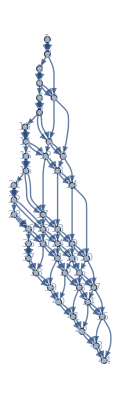
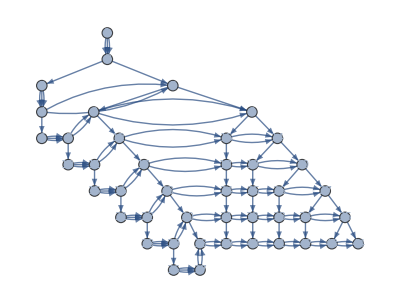
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics--Graphics--Graphics--Graphics3D-

```mathematica
SSSDisplay[sss, SSSMax->15,NetMethod->All]
```

Use SSSInteractiveDisplay to tweak the display options, click the "Save these options" button when satisfied:

```mathematica
SSSInteractiveDisplay[sss]
```

```mathematica
SSSDisplay[sss,Min->1,Max->44,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->350,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->0.8,VertexLabels->Placed[Automatic,Center],DirectedEdges->False]
```

Examples of using SSSAnimate:

```mathematica
SSSAnimate[sss, NetSize->400]
```

```mathematica
SSSAnimate[sss, VertexLabels->"VertexWeight", NetSize->400]
```

If you forget the syntax, ask for help (?):

```mathematica
?SSS
```

```mathematica
sss2=SSS[36660528645,100,Mode->Silent];
```

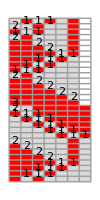
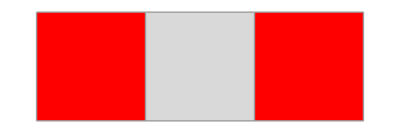

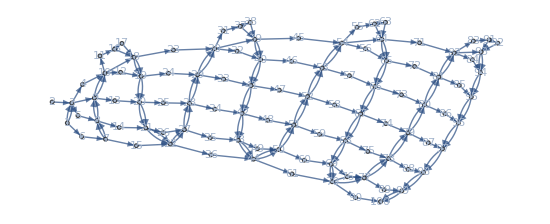
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss2,SSSMax->30,SSSSize->{100,200},NetSize->550]
```

### Examples of using the Reduced Enumeration:

Convert from an index (positive integer), a base-5 (quinary) code, or from an explicit set of rules.  All these return an ruleset object:

```mathematica
FromReducedRankIndex[236252479]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

```mathematica
FromReducedRankQuinaryCode["324323423242"]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

```mathematica
FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"A"}]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

The first 50 rulesets in the reduced enumeration:

```mathematica
Grid[
Prepend[
Values[FromReducedRankIndex[#]]&/@ Range[50],
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1 |  | {A→}
2 | 0 | {A→,→A}
3 | 1 | {A→,A→}
4 | 2 | {A→A}
5 | 3 | {AA→}
6 | 4 | {B→}
7 | 00 | {A→,→A,→,A→}
8 | 01 | {A→,→A,→A}
9 | 02 | {A→,→A,A→}
10 | 03 | {A→,→AA}
11 | 04 | {A→,→B}
12 | 10 | {A→,A→,→A}
13 | 11 | {A→,A→,A→}
14 | 12 | {A→,A→A}
15 | 13 | {A→,AA→}
16 | 14 | {A→,B→}
17 | 20 | {A→A,→,A→}
18 | 21 | {A→A,→A}
19 | 22 | {A→A,A→}
20 | 23 | {A→AA}
21 | 24 | {A→B}
22 | 30 | {AA→,→A}
23 | 31 | {AA→,A→}
24 | 32 | {AA→A}
25 | 33 | {AAA→}
26 | 34 | {AB→}
27 | 40 | {B→,→A}
28 | 41 | {B→,A→}
29 | 42 | {B→A}
30 | 43 | {BA→}
31 | 44 | {C→}
32 | 000 | {A→,→A,→,A→,→A}
33 | 001 | {A→,→A,→,A→,A→}
34 | 002 | {A→,→A,→,A→A}
35 | 003 | {A→,→A,→,AA→}
36 | 004 | {A→,→A,→,B→}
37 | 010 | {A→,→A,→A,→,A→}
38 | 011 | {A→,→A,→A,→A}
39 | 012 | {A→,→A,→A,A→}
40 | 013 | {A→,→A,→AA}
41 | 014 | {A→,→A,→B}
42 | 020 | {A→,→A,A→,→A}
43 | 021 | {A→,→A,A→,A→}
44 | 022 | {A→,→A,A→A}
45 | 023 | {A→,→A,AA→}
46 | 024 | {A→,→A,B→}
47 | 030 | {A→,→AA,→,A→}
48 | 031 | {A→,→AA,→A}
49 | 032 | {A→,→AA,A→}
50 | 033 | {A→,→AAA}

Or start anywhere:

```mathematica
Grid[Prepend[Values[FromReducedRankIndex[#]]&/@ (1181262395+Range[0,10]),
{"index","q-code","ruleset"}],Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1181262395 | 3243234232423 | {AA→BA,AB→AA,B→AA}
1181262396 | 3243234232424 | {AA→BA,AB→AA,B→B}
1181262397 | 3243234232430 | {AA→BA,AB→AA,BA→,→A}
1181262398 | 3243234232431 | {AA→BA,AB→AA,BA→,A→}
1181262399 | 3243234232432 | {AA→BA,AB→AA,BA→A}
1181262400 | 3243234232433 | {AA→BA,AB→AA,BAA→}
1181262401 | 3243234232434 | {AA→BA,AB→AA,BB→}
1181262402 | 3243234232440 | {AA→BA,AB→AA,C→,→A}
1181262403 | 3243234232441 | {AA→BA,AB→AA,C→,A→}
1181262404 | 3243234232442 | {AA→BA,AB→AA,C→A}
1181262405 | 3243234232443 | {AA→BA,AB→AA,CA→}

### Ruleset Tests: Explanations & Examples

All Test... functions expect an argument of the Association with Keys {"Index", "QCode", "RuleSet"}, and return {} (if not applicable) or resolution ruleset object.

#### TestForConflictingRules

A pair of conflicting rules occurs when two rules in the ruleset have the same left-hand side, or more generally, when the left-hand side of one rule is a substring of the left-hand side of a later rule. For example, consider the ruleset {"ABA"→"AAB", "ABA"→"", "A"→"ABA"} (# 158 448 842 380 in the RSS list, quinary code = 3432334234312343_5).  Here, rule 2 conflicts with rule 1, and will never be used.

Check rule by rule, starting with j = 2, see whether rule j conflicts with any previous rules.  If so, find the match that ends earliest in lhs j, and let rule i be the one that gave this match.  Stop on first match.

In the reduced enumeration of SSS rulesets we can "long-jump" past all rulesets sharing the initial part of the ruleset, including the conflicting rules.  (The resolution ruleset is the first that does not have the same problem:  it may have the first rule but does not have the second.)

Christen has convinced me that after every long-jump of this type, there will be a series of additional jumps due to creation rules, ending with the ruleset that has tailweight of appended As.  This means longer long-jumps!  Unfortunately there appears to be a different goal ruleset depending on whether the original match in the conflicting rules’ lhs is the empty string or something else, and if something else we still have two sub-cases, depending on whether the tailweight is 1 or more.  Rather than separately testing for these subcases, we will simply repeat the TestForConflictingRules, and the second test will always match an empty string, catching a (different) conflicting rules situation with a non-final creation rule.

Note: in an accelerated iteration through the Reduced SS enumeration, after every successful long-jump, we now plan to immediately perform a TestForConflictingRules!

Seeking an operation on the quinary codes justifies treating only two (2) cases:  (1) a conflicting rules case with a non-empty match,  (2) a conflicting rules case with an empty match string, “” (triggered by a ‘0’ or ‘1’ in the quinary code).  Only in the second case will we jump past the additional mini-jumps due to the creation rule.  For the first case, we actually set up a creation rule for the next application of the test to take care of, but it is a different problem.  This seems like extra work, but it is a minimalist strategy, in both cases we jump past the immediate problem, in the first we know that there will immediately be another problem, but it will be resolved without special treatment in one additional step.

non-creation case:  replace last tailweight digits of qcode by ‘4000...0’.  (Equivalent to:  keep all rules up to j-1, keep lhs of rule j up to but not including last character of match position,increment final character of match, use "" as rhs. Now spread out remaining weight as much as possible by filling up the quinary digits with 0s.  (Each 0 adds "", "", "A" to the ruleset.)

creation case:  replace last tailweight digits of the qcode by ‘3’s.  (Equivalent to:  keep rules up to j-2, append tailweight string of As to the rhs of rule j-1, stop)

Examples of RuleSet Tests:

```mathematica
FromReducedRankQuinaryCode["3432334234312343"]
TestForConflictingRules[%]
```

<|Index→158448842380,QCode→3432334234312343,RuleSet→{ABA→AAB,ABA→,A→ABA}|>

<|Index→158448843907,QCode→3432334234340000,RuleSet→{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24344234244"]
TestForConflictingRules[%]
```

<|Index→41106356,QCode→24344234244,RuleSet→{A→BC,AB→C}|>

<|Index→41106407,QCode→24344240000,RuleSet→{A→BC,B→,→A,→,A→,→A,→,A→}|>

```mathematica
Grid[
Prepend[
Values[FromReducedRankIndex[#]]&/@ (41106356+Range[0,51]),
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
41106356 | 24344234244 | {A→BC,AB→C}
41106357 | 24344234300 | {A→BC,ABA→,→A,→,A→}
41106358 | 24344234301 | {A→BC,ABA→,→A,→A}
41106359 | 24344234302 | {A→BC,ABA→,→A,A→}
41106360 | 24344234303 | {A→BC,ABA→,→AA}
41106361 | 24344234304 | {A→BC,ABA→,→B}
41106362 | 24344234310 | {A→BC,ABA→,A→,→A}
41106363 | 24344234311 | {A→BC,ABA→,A→,A→}
41106364 | 24344234312 | {A→BC,ABA→,A→A}
41106365 | 24344234313 | {A→BC,ABA→,AA→}
41106366 | 24344234314 | {A→BC,ABA→,B→}
41106367 | 24344234320 | {A→BC,ABA→A,→,A→}
41106368 | 24344234321 | {A→BC,ABA→A,→A}
41106369 | 24344234322 | {A→BC,ABA→A,A→}
41106370 | 24344234323 | {A→BC,ABA→AA}
41106371 | 24344234324 | {A→BC,ABA→B}
41106372 | 24344234330 | {A→BC,ABAA→,→A}
41106373 | 24344234331 | {A→BC,ABAA→,A→}
41106374 | 24344234332 | {A→BC,ABAA→A}
41106375 | 24344234333 | {A→BC,ABAAA→}
41106376 | 24344234334 | {A→BC,ABAB→}
41106377 | 24344234340 | {A→BC,ABB→,→A}
41106378 | 24344234341 | {A→BC,ABB→,A→}
41106379 | 24344234342 | {A→BC,ABB→A}
41106380 | 24344234343 | {A→BC,ABBA→}
41106381 | 24344234344 | {A→BC,ABC→}
41106382 | 24344234400 | {A→BC,AC→,→A,→,A→}
41106383 | 24344234401 | {A→BC,AC→,→A,→A}
41106384 | 24344234402 | {A→BC,AC→,→A,A→}
41106385 | 24344234403 | {A→BC,AC→,→AA}
41106386 | 24344234404 | {A→BC,AC→,→B}
41106387 | 24344234410 | {A→BC,AC→,A→,→A}
41106388 | 24344234411 | {A→BC,AC→,A→,A→}
41106389 | 24344234412 | {A→BC,AC→,A→A}
41106390 | 24344234413 | {A→BC,AC→,AA→}
41106391 | 24344234414 | {A→BC,AC→,B→}
41106392 | 24344234420 | {A→BC,AC→A,→,A→}
41106393 | 24344234421 | {A→BC,AC→A,→A}
41106394 | 24344234422 | {A→BC,AC→A,A→}
41106395 | 24344234423 | {A→BC,AC→AA}
41106396 | 24344234424 | {A→BC,AC→B}
41106397 | 24344234430 | {A→BC,ACA→,→A}
41106398 | 24344234431 | {A→BC,ACA→,A→}
41106399 | 24344234432 | {A→BC,ACA→A}
41106400 | 24344234433 | {A→BC,ACAA→}
41106401 | 24344234434 | {A→BC,ACB→}
41106402 | 24344234440 | {A→BC,AD→,→A}
41106403 | 24344234441 | {A→BC,AD→,A→}
41106404 | 24344234442 | {A→BC,AD→A}
41106405 | 24344234443 | {A→BC,ADA→}
41106406 | 24344234444 | {A→BC,AE→}
41106407 | 24344240000 | {A→BC,B→,→A,→,A→,→A,→,A→}

```mathematica
FromReducedRankQuinaryCode["434422434424224"]
TestForConflictingRules[%]
```

<|Index→36902752596,QCode→434422434424224,RuleSet→{BC→A,BC→B,A→B}|>

<|Index→36902753282,QCode→434422434440000,RuleSet→{BC→A,BD→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24144124234"]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2414434124234"]
TestForConflictingRules[%]
```

<|Index→1008211976,QCode→2414434124234,RuleSet→{A→B,→CB,→A,B→AB}|>

<|Index→1008218750,QCode→2414434333333,RuleSet→{A→B,→CBAAAAAA}|>

```mathematica
FromReducedRankIndex[321351]
TestForConflictingRules[%]
```

<|Index→321351,QCode→24124234,RuleSet→{A→B,→A,B→AB}|>

<|Index→321875,QCode→24133333,RuleSet→{A→B,→AAAAAA}|>

```mathematica
FromReducedRankIndex[8065101]
TestForConflictingRules[%]
```

<|Index→8065101,QCode→2414424234,RuleSet→{A→B,→C,B→AB}|>

<|Index→8065625,QCode→2414433333,RuleSet→{A→B,→CAAAAA}|>

```mathematica
FromReducedRankIndex[40321351]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankIndex[40328125]
TestForConflictingRules[%]
```

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

{}

```mathematica
FromReducedRankIndex[13267]
TestForConflictingRules[%]
```

<|Index→13267,QCode→244420,RuleSet→{A→D,A→,→A}|>

<|Index→13271,QCode→244424,RuleSet→{A→D,B→}|>

Examples from JCS paper:

```mathematica
FromReducedRankQuinaryCode["3432334234312343"]
TestForConflictingRules[%]
```

<|Index→158448842380,QCode→3432334234312343,RuleSet→{ABA→AAB,ABA→,A→ABA}|>

<|Index→158448843907,QCode→3432334234340000,RuleSet→{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24344234244"]
TestForConflictingRules[%]
```

<|Index→41106356,QCode→24344234244,RuleSet→{A→BC,AB→C}|>

<|Index→41106407,QCode→24344240000,RuleSet→{A→BC,B→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["434422434424224"]
TestForConflictingRules[%]
```

<|Index→36902752596,QCode→434422434424224,RuleSet→{BC→A,BC→B,A→B}|>

<|Index→36902753282,QCode→434422434440000,RuleSet→{BC→A,BD→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24144124234"]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2414434124234"]
TestForConflictingRules[%]
```

<|Index→1008211976,QCode→2414434124234,RuleSet→{A→B,→CB,→A,B→AB}|>

<|Index→1008218750,QCode→2414434333333,RuleSet→{A→B,→CBAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2404234"]
TestForConflictingRules[%]
```

<|Index→63851,QCode→2404234,RuleSet→{A→B,→,B→AB}|>

<|Index→64375,QCode→2413333,RuleSet→{A→B,→AAAAA}|>

#### TestForIdentityRule, TestForNonSoloIdentityRule

An identity rule occurs when the left-hand side of a rule is identical to the right-hand side of that same rule. A ruleset containing an identity rule and at least one other rule can be discarded, whether or not the identity rule is ever executed. For example, consider the ruleset {"A"→"CC", "B"→"B", "C"→"A"} (# 5 178 059 904 in RSS list, quinary code = 24434424242442_5). If the second rule is never executed, the behavior of the ruleset is equivalent to a simpler, previously considered one, without the identity rule: {"A"→"CC", "C"→"A"} (# 8 284 904, quinary code = 2443442442_5).  On the other hand, if the identity rule is executed once, the enumeration will go into an infinite loop of "B"→"B" and any later rules will never be executed afterwards.

TestForIdentityRule[rs] tests for any identity rule anywhere in the ruleset, TestForNonSoloIdentityRule tests for a ruleset containing an identity rule and at least one other (and is therefore discardable).  A solo identity rule is not a problem, but it will generate a simple single- or multiple-stranded chain -- depending on the length of the string in the rule.  Therefore at this point we may optionally discard out of hand all rulesets containing an identity rule, IF solo identity rules are considered separately.

The procedure for finding the resolution to an identity rule situation depends on whether it is a ""→"" rule or not.  In both cases we need to know w, the weight of the rules following the identity rule.  A "nothing to nothing" rule is created by a 0 in the quinary code (the instruction to end the current string, insert two empty strings, and start a new string with "A").  In this case, resolution is achieved by replacing the last w quinary digits by '1000...0'.  The '1' changes the "nothing to nothing" rule to a "nothing to something", and filling in with '0' digits ensures that no cases will be left out.  On the other hand, to jump past any other type of identity rule situation, we simply have to append an "A" to the rhs of the identity rule, which can be done by by replacing the last w quinary digits by '3000...0'.

TestForNonSoloIdentityRule does a preliminary check for singleton rulesets, returning {} if applicable, and only tests for identity rules otherwise.  This version would be used if singleton cases are of interest.  For example, the first single strand 1-d network is created by the ruleset {"A"→"A"}, the first double strand 1-d network by the ruleset {"AA"→"AA}.

```mathematica
TestForIdentityRule@FromReducedRankRuleSet@{"A"->"A"}
```

<|Index→5,QCode→3,RuleSet→{AA→}|>

```mathematica
TestForNonSoloIdentityRule@FromReducedRankRuleSet@{"A"->"A"}
```

{}

```mathematica
FromReducedRankRuleSet@{"A"->"BB","C"->"C","AA"->"B",""->"A"}
```

<|Index→25676111853,QCode→243424424423241,RuleSet→{A→BB,C→C,AA→B,→A}|>

```mathematica
TestForIdentityRule@%
```

<|Index→25676112032,QCode→243424424430000,RuleSet→{A→BB,C→CA,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankRuleSet@{"A"->"BB","C"->"C"}
TestForIdentityRule@%
```

<|Index→8216356,QCode→2434244244,RuleSet→{A→BB,C→C}|>

<|Index→8216357,QCode→2434244300,RuleSet→{A→BB,CA→,→A,→,A→}|>

```mathematica
FromReducedRankRuleSet@{"A"->"BB",""->"","B"->"A"}
TestForIdentityRule@%
```

<|Index→65679,QCode→2434042,RuleSet→{A→BB,→,B→A}|>

<|Index→65682,QCode→2434100,RuleSet→{A→BB,→A,→,A→,→A}|>

```mathematica
Grid[Prepend[Values[FromReducedRankIndex[#]]&/@ Range[65657-1,65682],
{"index","q-code","ruleset"}],Alignment->Left,Dividers->{None,{False,True}},Background->{Automatic,{3->LightPink,-4->LightPurple,-1->LightGreen}}]
```

index | q-code | ruleset
65656 | 2433444 | {A→BAD}
65657 | 2434000 | {A→BB,→,A→,→A,→,A→}
65658 | 2434001 | {A→BB,→,A→,→A,→A}
65659 | 2434002 | {A→BB,→,A→,→A,A→}
65660 | 2434003 | {A→BB,→,A→,→AA}
65661 | 2434004 | {A→BB,→,A→,→B}
65662 | 2434010 | {A→BB,→,A→,A→,→A}
65663 | 2434011 | {A→BB,→,A→,A→,A→}
65664 | 2434012 | {A→BB,→,A→,A→A}
65665 | 2434013 | {A→BB,→,A→,AA→}
65666 | 2434014 | {A→BB,→,A→,B→}
65667 | 2434020 | {A→BB,→,A→A,→,A→}
65668 | 2434021 | {A→BB,→,A→A,→A}
65669 | 2434022 | {A→BB,→,A→A,A→}
65670 | 2434023 | {A→BB,→,A→AA}
65671 | 2434024 | {A→BB,→,A→B}
65672 | 2434030 | {A→BB,→,AA→,→A}
65673 | 2434031 | {A→BB,→,AA→,A→}
65674 | 2434032 | {A→BB,→,AA→A}
65675 | 2434033 | {A→BB,→,AAA→}
65676 | 2434034 | {A→BB,→,AB→}
65677 | 2434040 | {A→BB,→,B→,→A}
65678 | 2434041 | {A→BB,→,B→,A→}
65679 | 2434042 | {A→BB,→,B→A}
65680 | 2434043 | {A→BB,→,BA→}
65681 | 2434044 | {A→BB,→,C→}
65682 | 2434100 | {A→BB,→A,→,A→,→A}

Examples from JCS paper:

```mathematica
FromReducedRankQuinaryCode["442222424344"]
TestForIdentityRule@%
```

<|Index→300299506,QCode→442222424344,RuleSet→{C→A,A→A,B→BC}|>

<|Index→300300782,QCode→442223000000,RuleSet→{C→A,A→AA,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["4234234323432243"]
TestForIdentityRule@%
```

<|Index→177199143605,QCode→4234234323432243,RuleSet→{B→AB,ABA→ABA,A→BA}|>

<|Index→177199143657,QCode→4234234323433000,RuleSet→{B→AB,ABA→ABAA,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["434424344224242344"]
TestForIdentityRule@%
```

<|Index→4613292513006,QCode→434424344224242344,RuleSet→{BC→BC,A→B,B→AC}|>

<|Index→4613292675782,QCode→434424344300000000,RuleSet→{BC→BCA,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["2404234"]
TestForIdentityRule@%
```

<|Index→63851,QCode→2404234,RuleSet→{A→B,→,B→AB}|>

<|Index→63907,QCode→2410000,RuleSet→{A→B,→A,→,A→,→A,→,A→,→A}|>

#### TestForRenamedRuleSet

If the characters used in the strings of the ruleset are permuted or replaced by other characters, the SSS will look the same up to a permutation of colors, and the causal network will be identical.  Such cases can be identified without generating the SSS, as follows:

Examine the characters of all the strings of the ruleset in order, one character at a time.  The first character must be “A” (else renaming could make it so -- a previously seen case), the first character that is not an “A” must be a “B”, and the first that is not “A” or “B” must be “C”, etc.  As soon as an offending  character is found, take the total weight of all further characters, and replace that number of quinary code digits by ‘4’. This gives the quinary code of the last ruleset having a too-large character (now with maximal weight) at the problem position and same pre-problem (sub)strings, so this is the last ruleset that can safely be discarded in a long-jump.  (The resolution ruleset is the next in the enumeration, found by incrementing the RSS index by 1.)

Return resolution ruleset object, as usual.  If the test is negative, return {} as usual.

Important note:  Although the renamed ruleset may actually have a greater weight than the original version, this jump is safe and will allow us to skip all but one version of each ruleset (up to a permutation of the characters themselves).  It is true that we may have to wait until later in the enumeration to find some interesting case, since the renaming process preserves ruleset length, not ruleset weight.  But the advantage of being able to jump over huge intervals is too good to be missed, and we can always later find the canonical representative, the lowest index of the possible renamings of any interesting case, using the function ToCanonical.

```mathematica
FromReducedRankQuinaryCode["24242"]
TestForRenamedRuleSet[%]
```

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|>

{}

There was no problem.

```mathematica
FromReducedRankQuinaryCode["42224"]
TestForRenamedRuleSet[%]
```

<|Index→3596,QCode→42224,RuleSet→{B→A,A→B}|>

<|Index→3907,QCode→000000,RuleSet→{A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@3906
```

<|Index→3906,QCode→44444,RuleSet→{F→}|>

Last problem ruleset had weight 6 (5 quinary digits), resolution is in the next weight class.

```mathematica
FromReducedRankQuinaryCode["244424442"]
TestForRenamedRuleSet[%]
```

<|Index→1658904,QCode→244424442,RuleSet→{A→D,D→A}|>

<|Index→1660157,QCode→300000000,RuleSet→{AA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@1660156
```

<|Index→1660156,QCode→244444444,RuleSet→{A→I}|>

Resolution involved appending an "A".

```mathematica
FromReducedRankQuinaryCode["34244422424"]
TestForRenamedRuleSet[%]
```

<|Index→50486771,QCode→34244422424,RuleSet→{AB→D,A→B,B→}|>

<|Index→50488282,QCode→34300000000,RuleSet→{ABA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@50488281
```

<|Index→50488281,QCode→34244444444,RuleSet→{AB→I}|>

Resolution involved appending an "A".

```mathematica
FromReducedRankQuinaryCode["2343244234344443"]
TestForRenamedRuleSet[%]
```

<|Index→123253532030,QCode→2343244234344443,RuleSet→{A→ABA,C→ABEA}|>

<|Index→123253532032,QCode→2343244234400000,RuleSet→{A→ABA,C→AC,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@123253532031
```

<|Index→123253532031,QCode→2343244234344444,RuleSet→{A→ABA,C→ABF}|>

Resolution involved incrementing the "B" in the rhs of rule 2.

```mathematica
FromReducedRankQuinaryCode["2343244234344444"]
TestForRenamedRuleSet[%]
```

<|Index→123253532031,QCode→2343244234344444,RuleSet→{A→ABA,C→ABF}|>

<|Index→123253532032,QCode→2343244234400000,RuleSet→{A→ABA,C→AC,→,A→,→A,→,A→,→A,→,A→}|>

Same resolution if we apply the test to the last problem case above.

#### TestForInitialSubstringRule, TestForNonSoloInitialSubstringRule

TestForInitialSubstringRule[rs] tests whether a ruleset begins with any substring rule: a rule in which a string is replaced by a string of which it is a substring, returning either the empty set (if first rule is not a substring rule) or (if applicable) the resolution ruleset to long-jump over the current subsequence of the enumeration that has the same problem.  If not solo, such a ruleset is effectively equivalent to one or the other of two lower-weight, previously seen rulesets:  omitting the problem substring rule, or omitting all rules that follow it.

In the case of a solo substring rule, such a ruleset produces the same causal network (although not the same SSS) as a simpler solo identity rule case:  e.g., {A→ABC} has the same causal network as {A→A}.  In any case initial substring rulesets can be discarded.  Note: as currently implemented, TestForInitialSubstringRule will rule out solo substring (and solo identity rules).  If these are explicitly desired, either use TestForNonSoloInitialSubstringRule instead, or treat the desired cases separately.  (Easily done: an identity rule of lhs string length n creates a chain where each node is linked n times to the subsequent node.  It's enough to consider {A→A}, {AA→AA}, {AAA→AAA}, ….  The choice of characters will not affect the network.

Note:  initial creation rules (although they appear only in the GSS enumeration, not the reduced enumeration), are a special case of initial substring rules, but they produce no causal networks: only cell creation, no destruction, and therefore no links.

```mathematica
FromReducedRankQuinaryCode["2433442424424424"]
TestForInitialSubstringRule[%]
```

<|Index→128230799521,QCode→2433442424424424,RuleSet→{A→BAC,B→C,C→B}|>

<|Index→128234863282,QCode→2434000000000000,RuleSet→{A→BB,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["342343442442"]
TestForInitialSubstringRule[%]
```

<|Index→252034904,QCode→342343442442,RuleSet→{AB→ABC,C→A}|>

<|Index→252035157,QCode→342344000000,RuleSet→{AB→AC,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["242342343442442"]
TestForInitialSubstringRule[%]
```

<|Index→25398519279,QCode→242342343442442,RuleSet→{A→B,AB→ABC,C→A}|>

{}

Not an initial substring case.

```mathematica
FromReducedRankRuleSet[{"AB"->"ABC"}]
```

<|Index→403256,QCode→34234344,RuleSet→{AB→ABC}|>

```mathematica
FromReducedRankQuinaryCode["34234344"]
TestForInitialSubstringRule[%]
TestForNonSoloInitialSubstringRule[%%]
```

<|Index→403256,QCode→34234344,RuleSet→{AB→ABC}|>

<|Index→403257,QCode→34234400,RuleSet→{AB→AC,→,A→,→A}|>

{}

```mathematica
FromReducedRankQuinaryCode["342342"]
TestForInitialSubstringRule[%]
TestForNonSoloInitialSubstringRule[%%]
```

<|Index→16129,QCode→342342,RuleSet→{AB→AB,A→}|>

<|Index→16131,QCode→342344,RuleSet→{AB→AC}|>

<|Index→16131,QCode→342344,RuleSet→{AB→AC}|>

An non-singleton initial identity rule case is also a non-solo initial substring case.

#### TestForShorteningRuleSet

If all of the rules shorten the state string, the SSS must inevitably die out when the rules cease to be applied, either when the state string has shrunk to zero length or possibly before.  In addition, if none of the rules lengthen the state string, and at least one of them shortens it, that shortening rule will eventually cease to be applied, and therefore the SSS reduces to a previously considered simpler one.  In either case we designate such a ruleset as a shortening ruleset, and it may be discarded without generating the SSS, although no long-jumps can be justified.  The following function tests whether this situation occurs:

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->""}
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"A"}
```

{}

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->"A"}
```

{}

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->""}
```

<|Index→522,QCode→2430,RuleSet→{A→BA,→,A→}|>

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"BC","B"->""}
```

{}

#### TestForUnbalancedRuleSet

If any letter appears in one or more left-hand side rule strings but not in any right-hand side rule string, or vice versa, we call the ruleset unbalanced.  The behavior of such a ruleset will always duplicate that of some simpler ruleset.  If the extra letter is on a LHS, the rule concerned can at most be executed a finite number of times until all initial occurrences of the letter are “used up”.  On the other hand, if the extra letter occurs in the RHS of some rule, additional unmoveable instances of the letter are produced whenever the rule is executed.  If the rule stops being used, the future behavior of the ruleset simplifies to that of a simpler ruleset, else it creates an infinite number of “barriers” in the state string, separating portions that are thereafter mutually unreachable.  Even two such regions cannot be active indefinitely, since our rulesets are finite.  From some point on the activity will be limited to one of the regions, and again the behavior becomes that of a simpler ruleset.  (Note:  TRY TO VERIFY THIS!)  These considerations allow the exclusion of unbalanced rulesets without the need for stepping through their evolution.

```mathematica
TestForUnbalancedRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->"A","A"->"C"}
```

<|Index→1627357,QCode→242422300,RuleSet→{A→B,B→A,AA→,→A,→,A→}|>

```mathematica
FromReducedRankIndex /@ (1627357+Range[-1,0])
```

{<|Index→1627356,QCode→242422244,RuleSet→{A→B,B→A,A→C}|>,<|Index→1627357,QCode→242422300,RuleSet→{A→B,B→A,AA→,→A,→,A→}|>}

#### ToLeastWeight, ToCanonical (first renamed duplicate in enumeration not skipped over)

The long jumps serve an important role in accelerating the loop through the enumeration, but it will sometimes skip over the first occurrence of a renamed duplicate.  For example, {“B” → “A”, “A” → “A”} has a lower weight than {“A” → “B”, “B” → “B”} and appears first in the full enumeration, but will be skipped over by the TestForRenamedRuleSet long jump.  The long jumps guarantee that only one example of each permutation of character names will be considered -- A Good Thing, but we may have to go farther in the loop before coming to a particular network of interest.  The following functions will then easily give the two main versions of interest:

```mathematica
ToCanonical[{"B"->"A","A"->"A"}]
ToLeastWeight@%
```

{A→B,B→B}

{B→A,A→A}

Return a ruleset object if given a ruleset object:

```mathematica
FromReducedRankRuleSet@{"B"->"A","A"->"A"}
ToCanonical@%
ToLeastWeight@%
```

<|Index→719,QCode→4222,RuleSet→{B→A,A→A}|>

<|Index→13021,QCode→242424,RuleSet→{A→B,B→B}|>

<|Index→719,QCode→4222,RuleSet→{B→A,A→A}|>

```mathematica
ToCanonical@%
```

<|Index→13021,QCode→242424,RuleSet→{A→B,B→B}|>

```mathematica
{"B"->"D","DA"->"AD","AD"->"AC","AC"->"CA","CA"->"BA"}
ToCanonical@%
ToLeastWeight[%]
RuleSetWeight /@ {%%%,%%,%}
```

{B→D,DA→AD,AD→AC,AC→CA,CA→BA}

{A→B,BC→CB,CB→CD,CD→DC,DC→AC}

{D→B,BA→AB,AB→AC,AC→CA,CA→DA}

{40,50,36}

```mathematica
{#,ToCanonical[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToCanonical"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToCanonical
{BB→BA,AA→AB,A→BA} | {AA→AB,BB→BA,B→AB}
{BAB→ABA,A→B,B→AA} | {ABA→BAB,B→A,A→BB}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToCanonical/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{17,17,18,21,19,18,22,28}

These indicate in which weight class the (long-jumping) iteration will find them.

```mathematica
RuleSetWeight/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}
```

{16,16,18,21,19,18,22,29}

```mathematica
{#,ToLeastWeight[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToLeastWeight"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToLeastWeight
{BB→BA,AA→AB,A→BA} | {BB→BA,AA→AB,A→BA}
{BAB→ABA,A→B,B→AA} | {BAB→ABA,A→B,B→AA}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToLeastWeight /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{16,16,18,21,19,18,22,28}

Only in first two cases would the (slow!) full enumeration find them one weight earlier.  Clearly for these examples and presumably for many other equally interesting cases, the exponentially accelerating loop has little cost for the huge benefits.

### Examples of iterating through the enumeration

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

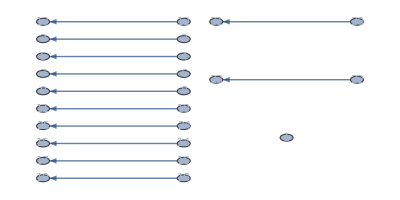
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|>

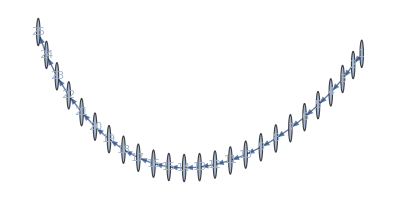
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→7,QCode→00,RuleSet→{A→,→A,→,A→}|>

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→8,QCode→01,RuleSet→{A→,→A,→A}|>

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9,QCode→02,RuleSet→{A→,→A,A→}|>

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|>

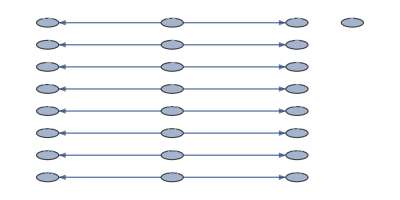
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
For[n=1,n≤10,n++,
sss=SSS[n,25,Mode->Silent];
If[sss["Verdict"]≠"Dead",
Print@FromReducedRankIndex[n];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->{50,100},NetSize->{400,200}]
]
]
```

### Accelerated iteration, using long-jumps

Note:  this loop uses the optimized order for invoking the tests

```mathematica
casesTreated=0;
rs=FromReducedRankIndex[1];  (* or other desired starting point in the enumeration *)
While[rs["Index"]<10^2,                                                           (* or some large number, stopping point *)
ans=TestForConflictingRules[rs];
If[Length[ans]>0,rs=ans;Continue[]];  (* if applicable, long-jump *)

ans=TestForNonSoloIdentityRule[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForRenamedRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForNonSoloInitialSubstringRule[rs];
If[Length[ans]>0,rs=ans;Continue[]];

(* tests that don't actually provoke long-jumps: *)

ans=TestForUnbalancedRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForShorteningRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

(* if none of the rules above applied, do something with rs here *) 

(* for example, just list the rulesets left to consider, counting them as we go *)
Print["# treated: ",++casesTreated," (",Round[100casesTreated/rs["Index"],.1],"%), n = ",rs["Index"], ": ",Subscript[rs["QCode"],5], ", ",rs["RuleSet"]];

(* finally, increment and loop *)
rs=FromReducedRankIndex[rs["Index"]+1]
]
```

# treated: 1 (50.%), n = 2: 0_5, {A→,→A}

# treated: 2 (50.%), n = 4: 2_5, {A→A}

# treated: 3 (30.%), n = 10: 03_5, {A→,→AA}

# treated: 4 (20.%), n = 20: 23_5, {A→AA}

# treated: 5 (22.7%), n = 22: 30_5, {AA→,→A}

# treated: 6 (12.%), n = 50: 033_5, {A→,→AAA}

### Accelerated iteration, using one combined long-jump test

<|Index→2,QCode→0,RuleSet→{A→,→A}|> (Repeating):

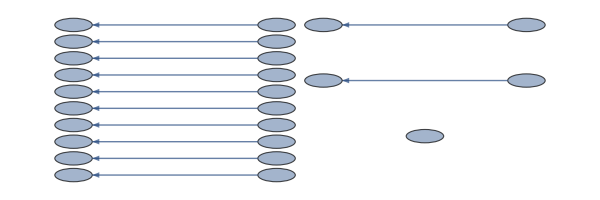
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|> (Repeating):

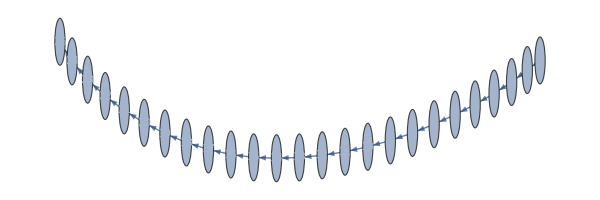
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|> (Repeating):

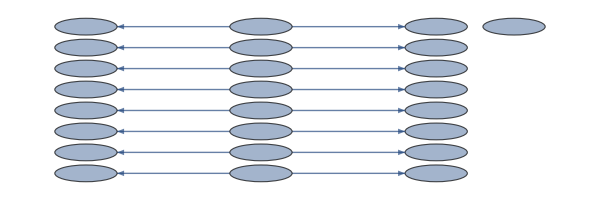
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→20,QCode→23,RuleSet→{A→AA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→22,QCode→30,RuleSet→{AA→,→A}|> (Repeating):

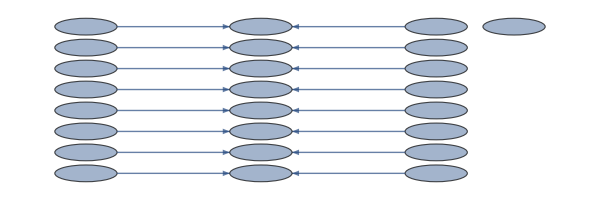
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50,QCode→033,RuleSet→{A→,→AAA}|> (Repeating):

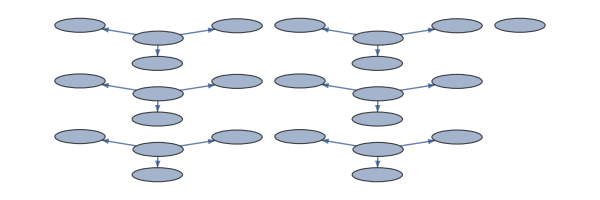
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→110,QCode→303,RuleSet→{AA→,→AA}|> (Repeating):

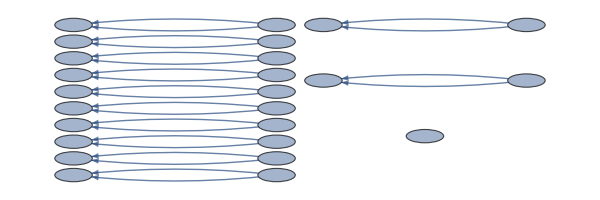
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→112,QCode→310,RuleSet→{AA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→118,QCode→321,RuleSet→{AA→A,→A}|> (Repeating):

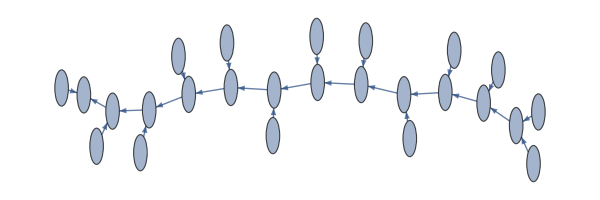
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→120,QCode→323,RuleSet→{AA→AA}|> (Repeating):

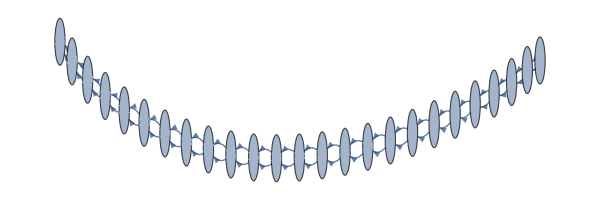
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→122,QCode→330,RuleSet→{AAA→,→A}|> (Repeating):

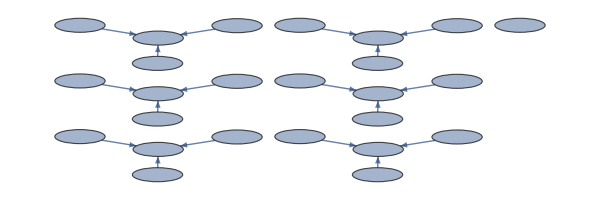
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→250,QCode→0333,RuleSet→{A→,→AAAA}|> (Repeating):

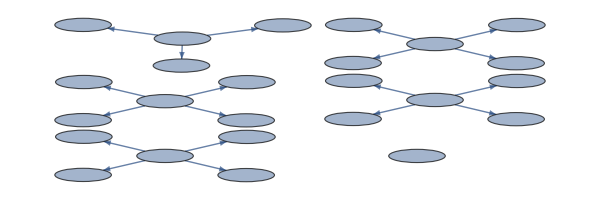
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→550,QCode→3033,RuleSet→{AA→,→AAA}|> (Repeating):

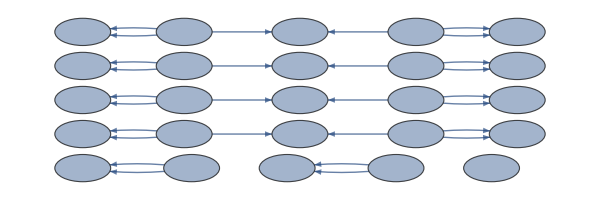
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→560,QCode→3103,RuleSet→{AA→,A→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→570,QCode→3123,RuleSet→{AA→,A→AA}|>: dead

<|Index→590,QCode→3213,RuleSet→{AA→A,→AA}|> (Repeating):

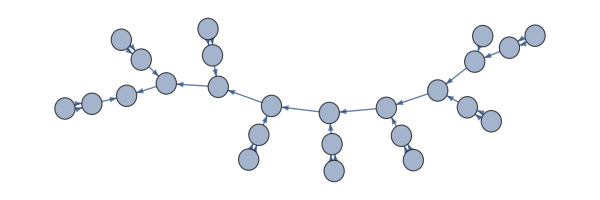
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→592,QCode→3220,RuleSet→{AA→A,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→600,QCode→3233,RuleSet→{AA→AAA}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→610,QCode→3303,RuleSet→{AAA→,→AA}|> (Repeating):

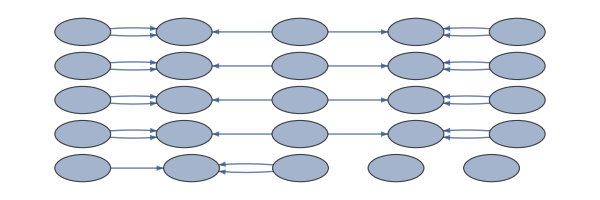
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→612,QCode→3310,RuleSet→{AAA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→618,QCode→3321,RuleSet→{AAA→A,→A}|> (Repeating):

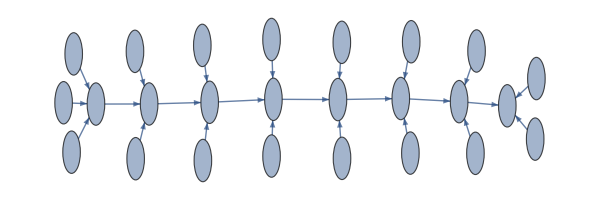
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→622,QCode→3330,RuleSet→{AAAA→,→A}|> (Repeating):

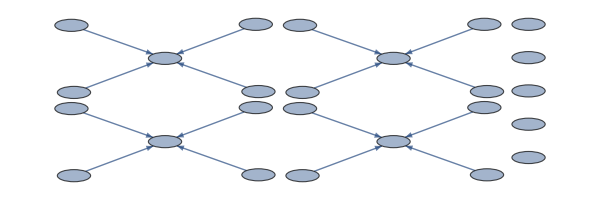
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1250,QCode→03333,RuleSet→{A→,→AAAAA}|> (Repeating):

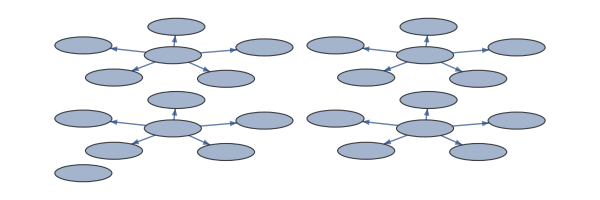
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1926,QCode→14034,RuleSet→{A→,B→,→AB}|> (Repeating):


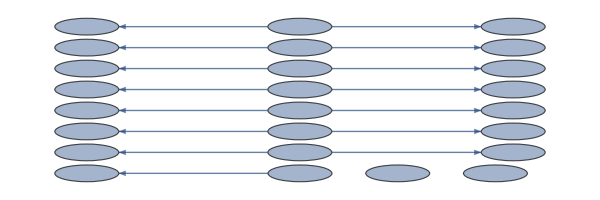
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1930,QCode→14043,RuleSet→{A→,B→,→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1966,QCode→14214,RuleSet→{A→,B→A,→B}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1976,QCode→14234,RuleSet→{A→,B→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1980,QCode→14243,RuleSet→{A→,B→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2602,QCode→24240,RuleSet→{A→B,B→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2750,QCode→30333,RuleSet→{AA→,→AAAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2800,QCode→31033,RuleSet→{AA→,A→,→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2848,QCode→31231,RuleSet→{AA→,A→AA,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2850,QCode→31233,RuleSet→{AA→,A→AAA}|>: dead

<|Index→2950,QCode→32133,RuleSet→{AA→A,→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2960,QCode→32203,RuleSet→{AA→A,A→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2970,QCode→32223,RuleSet→{AA→A,A→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3050,QCode→33033,RuleSet→{AAA→,→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3060,QCode→33103,RuleSet→{AAA→,A→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3070,QCode→33123,RuleSet→{AAA→,A→AA}|>: dead

<|Index→3072,QCode→33130,RuleSet→{AAA→,AA→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3090,QCode→33213,RuleSet→{AAA→A,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3092,QCode→33220,RuleSet→{AAA→A,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3098,QCode→33231,RuleSet→{AAA→AA,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3100,QCode→33233,RuleSet→{AAA→AAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3110,QCode→33303,RuleSet→{AAAA→,→AA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3112,QCode→33310,RuleSet→{AAAA→,A→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3118,QCode→33321,RuleSet→{AAAA→A,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3122,QCode→33330,RuleSet→{AAAAA→,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3176,QCode→34034,RuleSet→{AB→,→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3180,QCode→34043,RuleSet→{AB→,→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|> (OK):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3226,QCode→34234,RuleSet→{AB→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3228,QCode→34241,RuleSet→{AB→B,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3230,QCode→34243,RuleSet→{AB→BA}|>: dead

<|Index→6250,QCode→033333,RuleSet→{A→,→AAAAAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9626,QCode→140334,RuleSet→{A→,B→,→AAB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9630,QCode→140343,RuleSet→{A→,B→,→ABA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9650,QCode→140433,RuleSet→{A→,B→,→BAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9826,QCode→142134,RuleSet→{A→,B→A,→AB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9830,QCode→142143,RuleSet→{A→,B→A,→BA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9866,QCode→142314,RuleSet→{A→,B→AA,→B}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9876,QCode→142334,RuleSet→{A→,B→AAB}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9878,QCode→142341,RuleSet→{A→,B→AB,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9880,QCode→142343,RuleSet→{A→,B→ABA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9898,QCode→142431,RuleSet→{A→,B→BA,→A}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→9900,QCode→142433,RuleSet→{A→,B→BAA}|> (Repeating):

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
rs=FromReducedRankIndex[1];               (* or other desired starting point in the enumeration *)
While[rs["Index"]<10^4,                                                           (* or some large number, stopping point *)
If[(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[]];  (* skip all that we can *)

(* do something with the rulesets that are not skipped *)
sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
If[sss["Verdict"]==="Dead", Print[rs,": dead"],
(* else *) 
Print[rs," (",sss["Verdict"],"): "];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->{50,100},NetSize->{600,200},VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```